```mathematica
Switch[$OperatingSystem,
"MacOSX",$manchesterDir="/Users/garyanderson/git/manchesterCS/";$netBeansDir="/Users/garyanderson/NetBeansProjects/libSvmMac/",
"Windows",$manchesterDir="g:/git/manchesterCS/";
$netBeansDir="g:/NetBeansProjects/myLibsvm/",
"Unix",$manchesterDir="/msu/home/m1gsa00/git/manchesterCS/";
$netBeansDir="/msu/home/m1gsa00/NetBeansProjects/myLibsvm/"];
```

```mathematica
SetDirectory[$manchesterDir<>"61011/project"];
```

```mathematica
tryAR1$179=Import[$manchesterDir<>"61011/alenaMatlabCode/aBunch/ AR(1)TheTry$179$.mat"];
```

```mathematica
trycurve251=Import[$manchesterDir<>"61011/alenaMatlabCode/aBunch/ US curvatureTheTry$251$.mat"];
```

```mathematica
Needs["JLink`"];Needs["SVMR`"];
AddToClassPath[$netBeansDir<>"build/classes/"];
LoadJavaClass["libsvm.svm"];
```

```mathematica
allCX=tryAR1$179[[1]];allCY=Flatten[tryAR1$179[[2]]];
```

## One RHS Variable

0 -- linear: u’*v
	1 -- polynomial: (gamma*u’*v + coef0)^degree
	2 -- radial basis function: exp(-gamma*|u-v|^2)
	3 -- sigmoid: tanh(gamma*u’*v + coef0)

```mathematica
?Mini*
```

```mathematica
Get["SVMR`"]
```

practicalSelection::shdw: Symbol practicalSelection appears in multiple contexts {SVMR`,Global`}; definitions in context SVMR` may shadow or be shadowed by other definitions.

needs to include initial

```mathematica
practicalSelection[allCY,practicalEps[allCX,allCY,4]]
```

{0.0580734,0.00527223}

## linear

```mathematica
{slinear,mlinear,plinear,clinear}=doLinear[allCX=tryAR1$179[[1]],allCY=Flatten[tryAR1$179[[2]]],{.05,.0057},10];
forMinLinear[{cc_?NumberQ,eps_?NumberQ}]:=Norm[doLinear[allCX,allCY,{cc,eps},2][[4]]]
ha=NestList[doLinearStaelin @@ #&,{{{50,.5},forMinLinear[{50,.5}]},{{0.01,100},{0.00000001,1}},forMinLinear},30]
```

{{{{50,0.5},0.370056},{{0.01,100},{1.×10^-8,1}},forMinLinear},{{{0.01,0.5},0.370056},{{0.01,50.005},{0.25,0.75}},forMinLinear},{{{0.01,0.5},0.370056},{{0.01,25.0075},{0.375,0.625}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,12.5088},{0.375,0.5}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,6.25937},{0.375,0.4375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,3.13469},{0.375,0.40625}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,1.57234},{0.375,0.390625}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.791172},{0.375,0.382813}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.400586},{0.375,0.378906}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.205293},{0.375,0.376953}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.107646},{0.375,0.375977}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0588232},{0.375,0.375488}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0344116},{0.375,0.375244}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0222058},{0.375,0.375122}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0161029},{0.375,0.375061}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0130515},{0.375,0.375031}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0115257},{0.375,0.375015}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0107629},{0.375,0.375008}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0103814},{0.375,0.375004}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0101907},{0.375,0.375002}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0100954},{0.375,0.375001}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0100477},{0.375,0.375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0100238},{0.375,0.375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0100119},{0.375,0.375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.010006},{0.375,0.375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.010003},{0.375,0.375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0100015},{0.375,0.375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0100007},{0.375,0.375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0100004},{0.375,0.375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0100002},{0.375,0.375}},forMinLinear},{{{0.01,0.375},0.370056},{{0.01,0.0100001},{0.375,0.375}},forMinLinear}}

```mathematica
Dimensions[ha]
```

{31,3}

```mathematica
(*minRes={minVal,minSubs}=NMinimize[forMin[cc,eps],{cc,eps},Method->"RandomSearch"]*)
```

```mathematica
minRes={minVal,minSubs}={0.39616086860756466,{cc->5.4157761747928991,eps->0.0004387598640503337}}
```

{0.396161,{cc→5.41578,eps→0.00043876}}

```mathematica
{slinear,mlinear,plinear,clinear}=doLinear[allCX,Flatten[allCY],{cc,eps}/.minSubs,10];
```

0.000393451

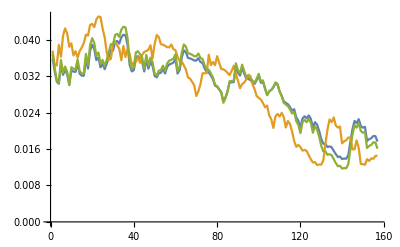

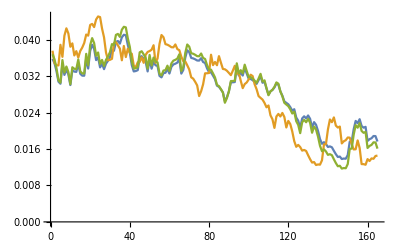

```mathematica
forLFit=ArrayFlatten[{{tryAR1$179[[1]],tryAR1$179[[2]]}}];
model=LinearModelFit[forLFit,xx,xx];
Norm[plinear-Flatten[allCY]]/Length[allCY]
(*svmtLinear=JavaNew["libsvm.trainGuts"];
svmtLinear[mmaUreadUproblemLinear[allCX,Flatten[allCY],{100,.01,10,.2,1}]];
modLinear=libsvm`svm`svmUtrain[svmtLinear[prob],svmtLinear[param]];*)svindLinear=mlinear[svUindices];
someLinear=(libsvm`svm`svmUpredict[mlinear,#1]&)/@allCX⟦svindLinear⟧;
somefitLin=(model)/@Flatten[allCX⟦svindLinear⟧];
ListLinePlot[{someLinear,allCY⟦svindLinear⟧,somefitLin}]
allLinear=libsvm`svm`svmUpredict[mlinear,#]&/@allCX;
allfitLin=(model)/@Flatten[allCX];
ListLinePlot[{allLinear,allCY,allfitLin}]
```

## poly

0.000392399

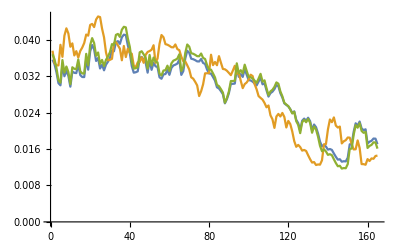

-Graphics-

```mathematica
{spoly,mpoly,ppoly,cpoly}=doPoly[allCX=tryAR1$179[[1]],allCY=Flatten[tryAR1$179[[2]]],{1000,8.273386262014822*^-6,1,.2,5},7];
forMinPoly[cc_?NumberQ,eps_?NumberQ,gamma_?NumberQ,coeff_?NumberQ,degree_?NumberQ]:=Norm[doPoly[allCX,Flatten[allCY],{cc,eps},2][[3]]];
Norm[ppoly-Flatten[allCY]]/Length[allCY]
svindPoly=mpoly[svUindices];
somePoly=(libsvm`svm`svmUpredict[mpoly,#1]&)/@allCX⟦svindPoly⟧;
somefitLin=(model)/@Flatten[allCX⟦svindPoly⟧];
ListLinePlot[{somePoly,allCY⟦svindPoly⟧,somefitLin}]
allPoly=libsvm`svm`svmUpredict[mpoly,#]&/@allCX;
allfitLin=(model)/@Flatten[allCX];
ListLinePlot[{allPoly,allCY,allfitLin}]
```

## RBF

0.000316386

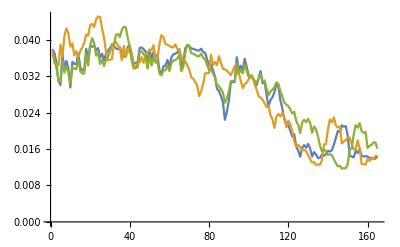

-Graphics-

```mathematica
{sRBF,mRBF,pRBF,cRBF}=doRBF[allCX=tryAR1$179[[1]],allCY=Flatten[tryAR1$179[[2]]],{1000,8.273386262014822*^-6,100,.2,5},7];
forMinRBF[cc_?NumberQ,eps_?NumberQ,gamma_?NumberQ,coeff_?NumberQ,degree_?NumberQ]:=Norm[doRBF[allCX,Flatten[allCY],{cc,eps},2][[3]]];Norm[pRBF-Flatten[allCY]]/Length[allCY]
svindRBF=mRBF[svUindices];
someRBF=(libsvm`svm`svmUpredict[mRBF,#1]&)/@allCX⟦svindRBF⟧;
somefitLin=(model)/@Flatten[allCX⟦svindRBF⟧];
ListLinePlot[{someRBF,allCY⟦svindRBF⟧,somefitLin}]
allRBF=libsvm`svm`svmUpredict[mRBF,#]&/@allCX;
allfitLin=(model)/@Flatten[allCX];
ListLinePlot[{allRBF,allCY,allfitLin}]
```

## Sigmoid

0.000394608

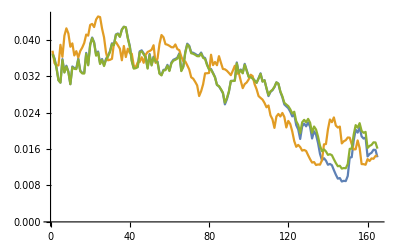

-Graphics-

```mathematica
{sSigmoid,mSigmoid,pSigmoid,cSigmoid}=doSigmoid[allCX=tryAR1$179[[1]],allCY=Flatten[tryAR1$179[[2]]],{1,8.273386262014822*^-6,100,.2,5},7];Norm[pSigmoid-Flatten[allCY]]/Length[allCY]
svindSigmoid=mSigmoid[svUindices];
someSigmoid=(libsvm`svm`svmUpredict[mSigmoid,#1]&)/@allCX⟦svindSigmoid⟧;
somefitLin=(model)/@Flatten[allCX⟦svindSigmoid⟧];
ListLinePlot[{someSigmoid,allCY⟦svindSigmoid⟧,somefitLin}]
allSigmoid=libsvm`svm`svmUpredict[mSigmoid,#]&/@allCX;
allfitLin=(model)/@Flatten[allCX];
ListLinePlot[{allSigmoid,allCY,allfitLin}]
```

## Comparisons

## Two RHS Variables

```mathematica
aFew=Range[20];
allCX=trycurve251[[1,All,{1,2}]];
allCY=Flatten[trycurve251[[2,All]]];
tryCX=allCX[[aFew,All]];
tryCY=allCY[[aFew]];
```

```mathematica
Dimensions[allCX]
```

{237,2}

doLinear expects num rows x = num elements y  features in columns original matlab has features in rows

## linear

```mathematica
{slinear,mlinear,plinear,clinear}=doLinear[allCX,allCY,{100,.001},10];
```

```mathematica
forMin[1,.01]
```

forMin[1,0.01]

```mathematica
forMin[cc_?NumberQ,eps_?NumberQ]:=Norm[doLinear[allCX,allCY,{cc,eps},2][[3]]]
```

```mathematica
(*NMinimize[forMin[cc,eps],{cc,eps},Method->"RandomSearch"]*)
```

```mathematica
minRes={minVal,minSubs}={0.39616086860756466,{cc->0.4157761747928991,eps->0.004387598640503337}}
```

{0.396161,{cc→0.415776,eps→0.0043876}}

```mathematica
{slinear,mlinear,plinear,clinear}=doLinear[allCX,allCY,{cc,eps}/.minSubs,10];
```

```mathematica
Norm[plinear-Flatten[allCY]]/Length[allCY]
```

0.000505712

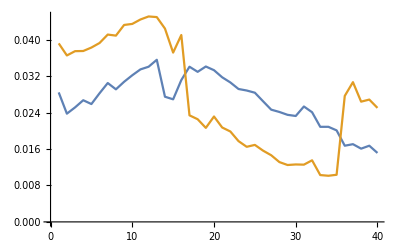

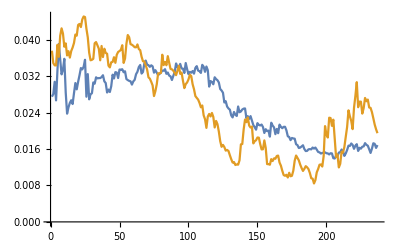

```mathematica
svmtLinear=JavaNew["libsvm.trainGuts"];
svmtLinear[mmaUreadUproblemLinear[allCX,allCY,{100,.01,10,.2,1}]];
modLinear=libsvm`svm`svmUtrain[svmtLinear[prob],svmtLinear[param]];svindLinear=modLinear[svUindices];
someLinear=(libsvm`svm`svmUpredict[modLinear,#1]&)/@allCX⟦svindLinear⟧;
ListLinePlot[{someLinear,allCY⟦svindLinear⟧}]
allLinear=libsvm`svm`svmUpredict[modLinear,#]&/@allCX;
ListLinePlot[{allLinear,allCY}]
```

## poly

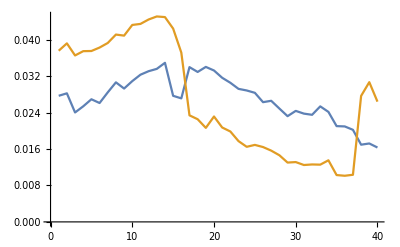

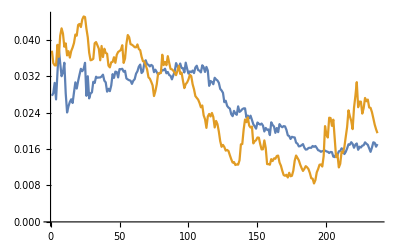

```mathematica
svmtPoly=JavaNew["libsvm.trainGuts"];
svmtPoly[mmaUreadUproblemPoly[allCX,Flatten[allCY],{100,.01,10,.2,1}]];
modPoly=libsvm`svm`svmUtrain[svmtPoly[prob],svmtPoly[param]];svindPoly=modPoly[svUindices];
somePoly=(libsvm`svm`svmUpredict[modPoly,#1]&)/@allCX⟦svindPoly⟧;
ListLinePlot[{somePoly,allCY⟦svindPoly⟧}]
allPoly=libsvm`svm`svmUpredict[modPoly,#]&/@allCX;
ListLinePlot[{allPoly,allCY}]
```

## RBF

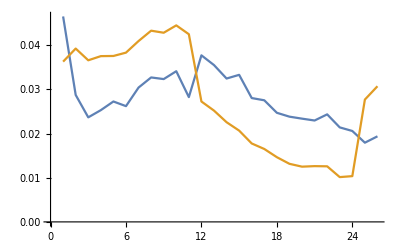

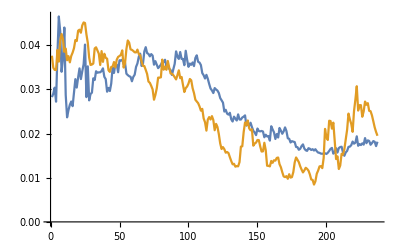

```mathematica
svmtRBF=JavaNew["libsvm.trainGuts"];
svmtRBF[mmaUreadUproblemRBF[allCX,Flatten[allCY],{100,.01,10,.2,1}]];
modRBF=libsvm`svm`svmUtrain[svmtRBF[prob],svmtRBF[param]];svindRBF=modRBF[svUindices];
someRBF=(libsvm`svm`svmUpredict[modRBF,#1]&)/@allCX⟦svindRBF⟧;
ListLinePlot[{someRBF,allCY⟦svindRBF⟧}]
allRBF=libsvm`svm`svmUpredict[modRBF,#]&/@allCX;
ListLinePlot[{allRBF,allCY}]
```

## Sigmoid

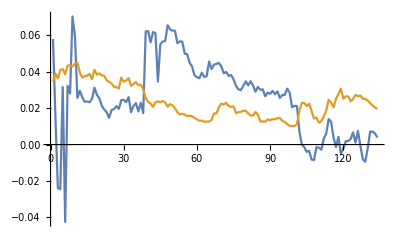

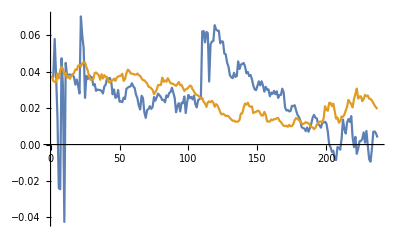

```mathematica
svmtSigmoid=JavaNew["libsvm.trainGuts"];
svmtSigmoid[mmaUreadUproblemSigmoid[allCX,Flatten[allCY],{10,.01,10,.2,1}]];
modSigmoid=libsvm`svm`svmUtrain[svmtSigmoid[prob],svmtSigmoid[param]];svindSigmoid=modSigmoid[svUindices];
someSigmoid=(libsvm`svm`svmUpredict[modSigmoid,#1]&)/@allCX⟦svindSigmoid⟧;
ListLinePlot[{someSigmoid,allCY⟦svindSigmoid⟧}]
allSigmoid=libsvm`svm`svmUpredict[modSigmoid,#]&/@allCX;
ListLinePlot[{allSigmoid,allCY}]
```